```mathematica
func2[x_,a_,P_]:=P (1.00-a^x) (*P is power aim, a determines rate*)
```

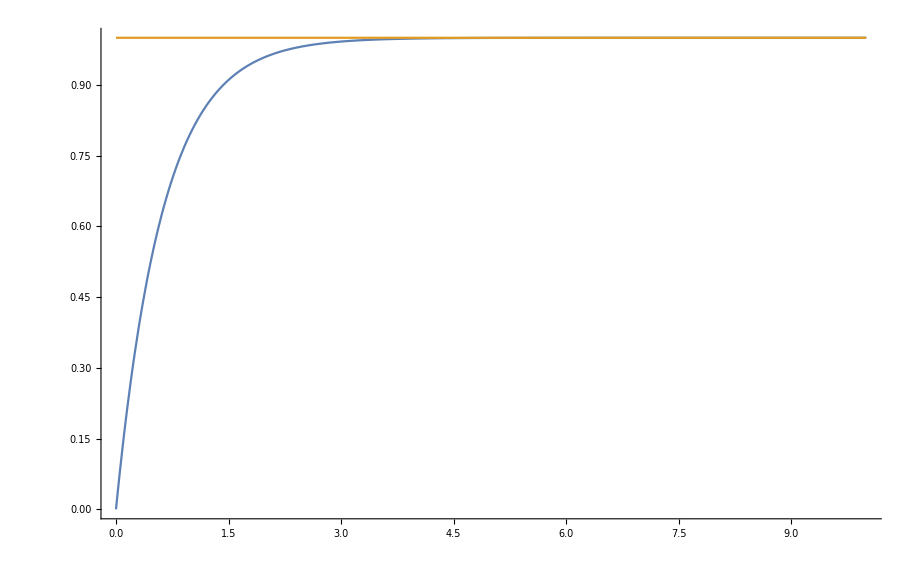

```mathematica
Plot[{func2[x,0.2,1], 1}, {x,0,10}, PlotRange->All]
```

```mathematica
pulsestoreachpower=600; (*should be total pulses rather than time*)
```

```mathematica
funcmax[percent_,a_]:=(Log10[1-percent/100])/(Log10[a])(*x value that gives a certain percentage of power required*)
```

```mathematica
steppulses=5;(*pulses at each power step*)
```

```mathematica
nsteps=pulsestoreachpower/steppulses;
```

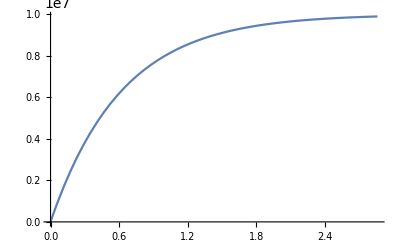

```mathematica
Plot[func2[x,0.2,1*^7], {x,0,funcmax[99,0.2]}] (*plot of function up to 99 percent of 10 MW*)
```

```mathematica
xsteps=Drop[Range[0,funcmax[99,0.2], funcmax[99,0.2]/(nsteps)],1];
```

```mathematica
ysteps[a_,P_]:=func2[#,0.2,1*^7]&/@xsteps
```

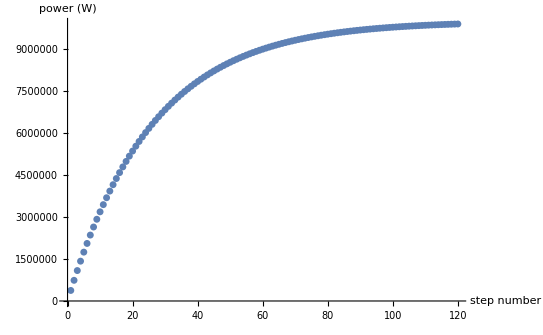

```mathematica
ListPlot[ysteps[0.2,1*^7], AxesLabel->{"step number","power (W)" }] (*Plot of function against step number, with 5 pulses at each step*)
```

```mathematica
repeat[list_,n_]:=Sequence@@ConstantArray[#,n]&/@list
```

```mathematica
repeat[func2[#,0.1,1*^7]&/@xsteps,steppulses];
```

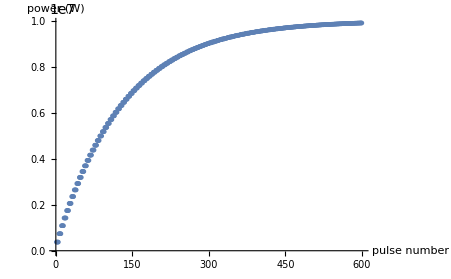

```mathematica
ListPlot[repeat[ysteps[0.2,1*^7],steppulses],AxesLabel->{"pulse number","power (W)" }](*Same plot as above but against pulse number*)
```